# Remainders Analysis

```mathematica
(*Imports*)
Needs["ErrorBarPlots`"];
(*Preliminaries*)
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Data", "PeriodFitData"}] ];

(*Period formula*)
truePeriod [slope_, periodGuess_]:=periodGuess/(1-slope);
σtruePeriod[slopes_, periodGuess_,σslopes_]:= 1/(1/periodGuess-slopes)^2*σslopes;

(*Pulsar name*)
pulsarName = "B2020+28";
```

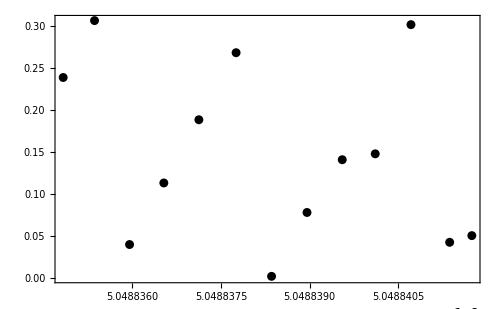

```mathematica
(*Estimated Period*)
periodGuess = 0.343402;

(*Import Data*)
times = ReadList[pulsarName <>"_times.txt", Number];
remainders= ReadList[pulsarName <>"_remainders.txt", Number];
σremainders= ReadList[pulsarName <>"_errors.txt", Number];

(*Organise data and do plot it as a check*)
data = Transpose[{times, remainders}];
plotData  = ParallelTable[{data[[i]],ErrorBar[σremainders[[i]]]},{i,1,Length@remainders}];
ErrorListPlot[plotData, PlotRange->All, Frame->True, ImageSize->500, PlotStyle->{Black, Thick}]
```

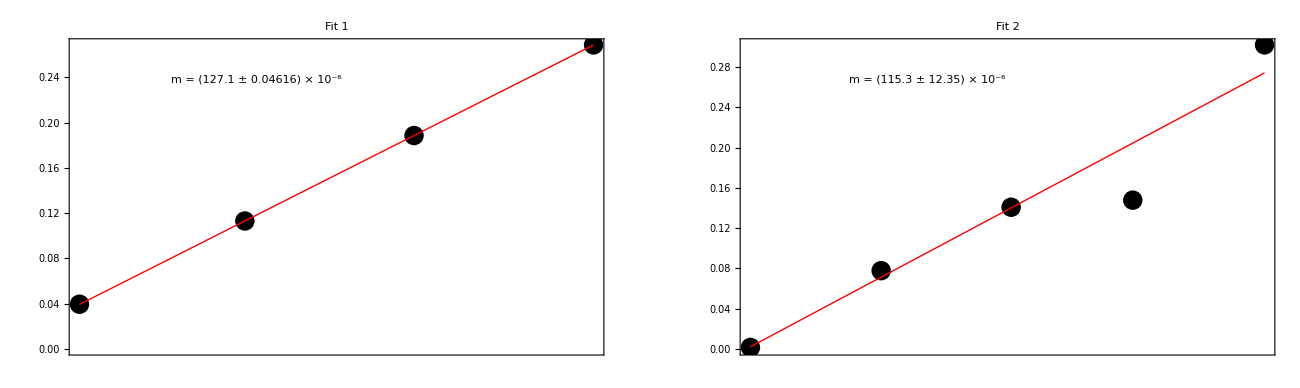

χ^2 values: {3.4357×10^-8,0.0040309}

Reduced χ^2 values: {1.7179×10^-8,0.0013436}

The probability of getting this χ^2: P = {1.,0.999932}

```mathematica
(*Separate data into full periods*)
peaksIdxs = FindPeaks[remainders][[All,1]];
sepData =ParallelTable[data[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,1,Length@peaksIdxs - 1}];
σsepData = ParallelTable[σremainders[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,1,Length@peaksIdxs - 1}];

(*For each period, find slopes, errors and the residuals*)
lms = ParallelTable[LinearModelFit[sepData[[i]],x,x, Weights->1/σsepData[[i]]^2],{i,1,Length@sepData}];
slopes = Table[lms[[i]]["BestFitParameters"][[2]], {i,1,Length@sepData}];
σslopes = Table[lms[[i]]["ParameterErrors"][[2]], {i,1,Length@sepData}];
residuals = Table[lms[[i]]["FitResiduals"], {i,1,Length@sepData}];

(*Fit statistics*)
nDof = Table[Length@sepData[[i]]-2,{i,1, Length@sepData}];
χsq = ParallelTable[Total[(residuals[[i]])^2],{i,1,Length@residuals}];
p=ParallelTable[Integrate[(E^(-χs/2)*χs^(nDof[[i]]/2-1))/(2^(nDof[[i]]/2)*Gamma[nDof[[i]]/2]),{χs,χsq[[i]],Infinity}],{i,1, Length@χsq}];

(*All plots and fits*)
xdata = ParallelTable[sepData[[i]][[All,1]],{i,1,Length@sepData}];
plots = ParallelTable[Show[ListPlot[sepData[[i]],PlotStyle->{Black,PointSize[0.02]}], Plot[lms[[i]][x],{x, Min[xdata[[i]]], Max[xdata[[i]]]}, PlotRange->All, PlotStyle->{Red, Thick}], Frame->True, ImageSize->700, PlotLabel->"Fit "<>ToString@i , LabelStyle->Directive[20],FrameTicks->{{Automatic,None},{None,None}}, FrameTicksStyle->{Directive[20],Directive[12]}, Epilog->{ Inset[Framed[Text[Style["m = (" <> ToString@NumberForm[slopes[[i]]*10^6,4] <> " ± " <>ToString@NumberForm[σslopes[[i]]*10^6,4] <> ") × 10^-6",FontFamily->Times, FontSize->12]], RoundingRadius->2], Scaled[{0.35,0.87}]]}],{i,1,Length@sepData}];
gridPlots = Partition[plots,UpTo[3]];

(*Outputting the results*)
grid = GraphicsGrid[gridPlots,ImageSize->1300, PlotLabel->pulsarName <> "\n", LabelStyle->Directive[25,Bold]]

Text[Row[{Style["χ^2 values:", Bold]," ", NumberForm[χsq,5]}]] 
Text[Row[{Style["Reduced χ^2 values:", Bold]," ", NumberForm[χsq/nDof,5]}]]  
Text[Row[{Style["The probability of getting this χ^2:", Bold]," P = ",p}]]
```

```mathematica
(*Get rid of bad slopes*)
newSlopes = Delete[slopes,2];
newσSlopes = Delete[slopes,2];

(*Calculate the periods*)
periods = Table[truePeriod[newSlopes[[i]],periodGuess],{i,1,Length@newSlopes}];
σperiods = σtruePeriod[newSlopes, periodGuess,newσSlopes];

(*Compute period*)
Period = periods[[1]];
σPeriod = σperiods[[1]];

toExportPeriod = OutputForm[CForm[Period]];
toExportσPeriod = OutputForm[CForm[Period]];
Export[pulsarName <> "_period.txt", {toExportPeriod,toExportσPeriod}];

(*Display Results*)
Text[Row[{Style["Mean Period:", Bold]," ", NumberForm[Period,20]}]]
Text[Row[{Style["Error on Mean Period:", Bold]," ", NumberForm[Period,20]}]]
```

Mean Period: 0.3434456571576439

Error on Mean Period: 0.3434456571576439

## Fitting one straight line

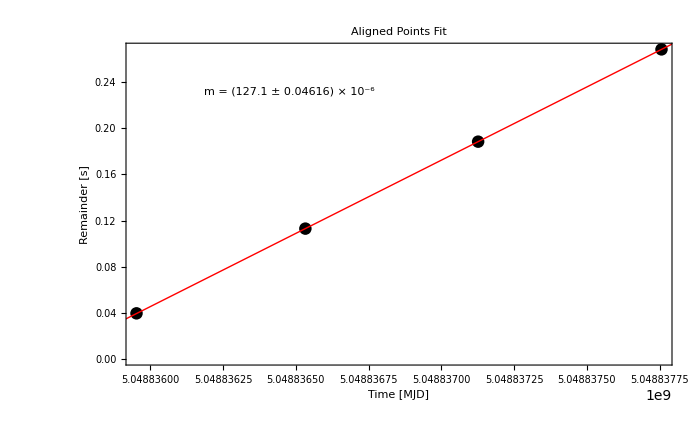

Period: 0.3434456571576439

Period Error: 5.444340092707865×10^-9

```mathematica
(*Aligning the lines*)
sepRemainders =ParallelTable[remainders[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,1,Length@peaksIdxs - 1}];
newTimes = Flatten[Table[times[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,1,Length@peaksIdxs - 2}]];
newRemainders = Flatten[Table[sepRemainders[[i]]+(i-1)*periodGuess,{i,1,Length@sepRemainders-1}]];
newData = Transpose[{newTimes, newRemainders}];
σnewData = σremainders[[peaksIdxs[[1]]+1 ;; peaksIdxs[[2]] ]];

(*Fittng data*)
lm = LinearModelFit[newData,x,x, Weights->1/σnewData^2];

(*Getting Quantities of the Fit*)
slope = lm["BestFitParameters"][[2]];
σslope = lm["ParameterErrors"][[2]];

(*Getting the period from the slope and guess*)
newPeriod = truePeriod[slope,periodGuess];
σnewPeriod = σtruePeriod[slope, periodGuess, σslope];

toExportnewPeriod = OutputForm[CForm[newPeriod]];
toExportσnewPeriod = OutputForm[CForm[σnewPeriod]];
Export[pulsarName <> "_periodalt.txt", {toExportnewPeriod,toExportσnewPeriod}];

(*Plot the fit*)
newPlotData = ParallelTable[{newData[[i]], ErrorBar[σnewData[[i]]]},{i,1,Length@newData}];
Show[ErrorListPlot[newPlotData, PlotStyle->{Black}], Plot[lm[x],{x,Min[times],Max[times]},PlotStyle->{Red, Thick}] ,Frame->True, ImageSize->700, PlotLabel->"Aligned Points Fit", FrameLabel->{"Time [MJD]","Remainder [s]"}, LabelStyle->Directive[20], FrameStyle->{Directive[20],Directive[15]},Epilog->{ Inset[Framed[Text[Style["m = (" <> ToString@NumberForm[slope*10^6,4] <> " ± " <>ToString@NumberForm[σslope*10^6,4] <> ") × 10^-6",FontFamily->Times, FontSize->18]], RoundingRadius->2], Scaled[{0.30,0.85}]]}]

(*Display Results*)
Text[Row[{Style["Period:", Bold]," ", NumberForm[newPeriod,20]}]]
Text[Row[{Style["Period Error:", Bold]," ", NumberForm[σnewPeriod,20]}]]
```